# Off-shell photon to distop decay

## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
<<FeynArts`
<<FormCalc`
```

FeynArts 3.10 (11 Jul 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (16 Apr 2018)

by Thomas Hahn

## Diagram Creation

> Top. 1 ad/bdcd/0.m, 1 diagram

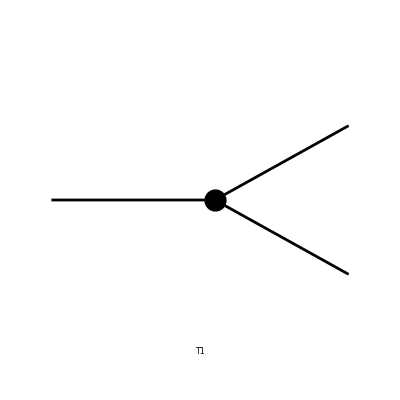

```mathematica
topo1=CreateTopologies[0,1->2,ExcludeTopologies->{Internal}];
Paint[topo1];
```

loading generic model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/MSSM.mod

> 94 particles (incl. antiparticles) in 23 classes

> $CounterTerms are ON

> 383 vertices

classes model {MSSM} initialized

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ad/bdcd/0.m, 1 diagram

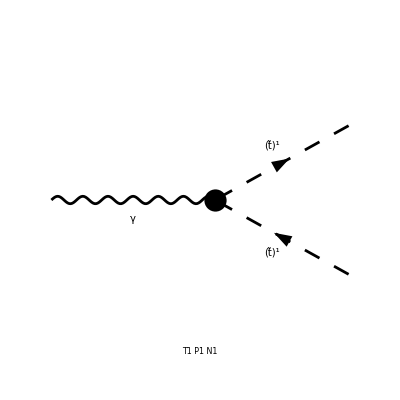

```mathematica
diag1=InsertFields[topo1,{V[1]}->{S[13,{1,3}],-S[13,{1,3}]},InsertionLevel->{Particles},Model->"MSSM"];
Paint[diag1];
```

## Generate Amplitude

```mathematica
ClearProcess[];
amp=CalcFeynAmp[OffShell[CreateFeynAmp[diag1],1->mOG],FermionChains->Chiral]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

preparing FORM code in /home/paul/projects/physics/Research/fc-amp-3.frm

running FORM...

ok

Amp((V(1) | k(1) | mOG | {})→(S(13,{1,3,Col2}) | k(2) | MSf(1,3,3) | {(2 Charge)/3,(2 ColorCharge)/(√3)}
-S(13,{1,3,Col3}) | k(3) | MSf(1,3,3) | {-(2 Charge)/3,-(2 ColorCharge)/(√3)}))(-4/3 EL Pair1 Mat(SUN1))

#### Check divergent piece

```mathematica
UVDivergentPart[amp]
divergence=%[[1]]
```

Amp((V(1) | k(1) | mOG | {})→(S(13,{1,3,Col2}) | k(2) | MSf(1,3,3) | {(2 Charge)/3,(2 ColorCharge)/(√3)}
-S(13,{1,3,Col3}) | k(3) | MSf(1,3,3) | {-(2 Charge)/3,-(2 ColorCharge)/(√3)}))(0)

0

#### Prepare for simplification

Note: polarization sum auto squares the matrix element

```mathematica
mat=(1/2)PolarizationSum[amp,GaugeTerms->False]//.Subexpr[]//.Abbr[]//Simplify
```

HelicityME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /home/paul/projects/physics/Research/fc-pol-3.frm

running FORM...

ok

8/3 π Alfa (mOG^2-4 MSf2(1,3,3))

## Numerical Evaluation

```mathematica
VALUES[stopMass1_,stopMass2_,xt_,mu_,alpha_,beta_]:={
Den[p2_,m2_]:>1/(p2-m2),
MT->173,MT2->173^2,
MW->80.4,MW2->80.4^2,
MZ-> 91.2,MZ2-> (91.2)^2,
Mh0-> 125,Mh02->(125)^2,
Alfa->1/128,Alfa2->1/128^2,
SW2->0.23,CW-> (MW/MZ),CW2->(MW/MZ)^2,
α-> alpha,β-> beta,MUE-> mu,MUEC -> mu,
CA->Cos[α],SB->Sin[β],SA->Sin[α],
SB2->(Sin[β])^2,SAB->Sin[α+β],
thetat-> (1/2)(ArcSin[(-2*MT*xt)/(stopMass2^2-stopMass1^2)]),
MSf[1,3,x_]->stopMass1,MSf2[1,3,x_]->stopMass1^2,
MSf[2,3,x_]->stopMass2,MSf2[2,3,x_]->stopMass2^2,
Af[3,3,3]-> ((xt/MT)+MUE*Cot[β]),AfC[3,3,3]-> ((xt/MT)+MUE*Cot[β]),
USfC[x_,y_,3,3]-> USf[x,y,3,3],USf[1,1,3,3]->Cos[thetat] ,USf[1,2,3,3]->Sin[thetat]}
MyMatrixElement[stopMass1_,stopMass2_,xt_,mu_,alpha_,beta_]:=mat//.VALUES[stopMass1,stopMass2,xt,mu,alpha,beta]//Simplify
```

```mathematica
MyMatrixElement[250,1000,0,250,-0.1008,1.47]
```

1/48 π (mOG^2-250000)

```mathematica
feynCalcResult = %/.mOG-> 600
```

(6875 π)/3

## Gamma to distop

```mathematica
matrixEl = -(8/9)*Pi*Alfa*(4*m^2 - mOG^2)
```

-8/9 π Alfa (4 m^2-mOG^2)

## Plug in values and compare to FeynArts result

```mathematica
matToSub =matrixEl//. ghSS-> h11
```

-8/9 π Alfa (4 m^2-mOG^2)

```mathematica
SUBIN[stopMass1_,stopMass2_,xt_,mu_,beta_]:={
mt->173,
mW->80.4,
mZ-> 91.2,
mh-> 125,
Alfa->1/128,Alfa2->(1/128)^2,
sW->0.4796,cW-> (mW/mZ),
β-> beta,μ-> mu,
thetat-> (1/2)(ArcSin[(-2*mt*xt)/(stopMass2^2-stopMass1^2)]),
e-> Sqrt[(4*Pi*Alfa)],
m->stopMass1,
At-> ((xt/mT)+μ*Cot[β]),
ct->Cos[thetat] ,st->Sin[thetat]}
MyResults[stopMass1_,stopMass2_,xt_,mu_,beta_]:=matToSub//.SUBIN[stopMass1,stopMass2,xt,mu,beta]//Simplify
```

```mathematica
MyResults[250,1000,0,250,1.47]
```

1/144 π (mOG^2-250000)

```mathematica
myResult = % /. mOG -> 600
```

(6875 π)/9

```mathematica
%*3
```

(6875 π)/3

```mathematica
myResult*3/feynCalcResult
```

1